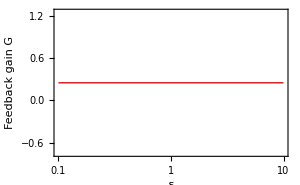

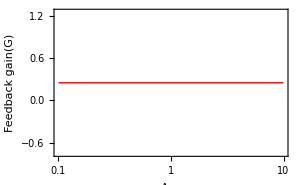

```mathematica
(*
This is part of the manuscript titled "Feedback-mediated circulation and persistence of stochastic fluctuations in gene
regulatory circuits" ;

Correspondence with the paper;

Please note ;
1. The four TNF motifs: Double positive feedback (++), Double negative feedback (--), Negative positive feedback (-+) and Positive negative feedback (+-);
2. αx and αy are production rates of X and Y;
3. βx and βy are degradation rates of X and Y;
4. fx=αx*gx, fy=αy*gy are the Hill functions with Hill coefficient=1;
5. xdot and ydot are the dynamical equations of X and Y;
6. xav=<x>, yav=<y> ;
7. fxyp = ∂fx/∂y and fyxp=∂fy/∂x are steady-state regulatory sensitivities;
8. G = H (feedback gain);
9. τxy and τyx are time-averaging factors;
10. δ is feedback strength and aτ is time-scale asymmetry;
11. The data is exported and plotted in another software
====================================================================== 
*)


(* Double Positive Feedback *)

gx=y/(y+Kyx);gy=x/(x+Kxy); (*Functions*)

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];
(*fixed points*)
xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fx=αx*gx; fy=αy*gy;

fxyp=αx*Kyx/(yav+Kyx)^2;fyxp=αy*Kxy/(xav+Kxy)^2;(*Derivative of functions fx, fy*)

G=(fxyp*fyxp)/(βx*βy); (*Feedback gain*)

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

LogLinearPlot[{G},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Feedback gain G"},ImageSize->300,PlotRange->All]
t13=Table[{δ,G},{δ,δi,δf,0.01}];
tp13=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"\n"]&/@t13];
(*Export["D:\\nashitarahman\\DP13g.dat",tp13,"FieldSeparators"->"    "];*)

Clear[βx,βy,Kxy,Kyx];

(*Parameters*)
βx=0.1*Sqrt[aτ]; βy=0.1/Sqrt[aτ];
Kyx=50; Kxy=50;

aτi=0.1;aτf=10;

LogLinearPlot[{G},{aτ,aτi,aτf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"A_τ","Feedback gain(G)"},ImageSize->300,PlotRange->All]
t14=Table[{aτ,G},{aτ,aτi,aτf,0.01}];
tp14=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"\n"]&/@t14];
(*Export["D:\\nashitarahman\\DP14g.dat",tp14,"FieldSeparators"->"    "];*)

Quit[];
```

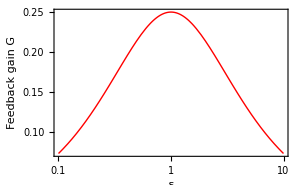

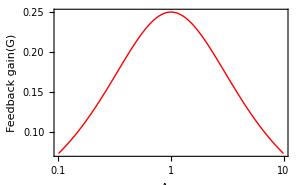

```mathematica
(*Double negative feedback*)
gx=Kyx/(y+Kyx);gy=Kxy/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[1,1]];
yav=y/.sol[[1,2]];

fxyp=-αx*Kyx/(yav+Kyx)^2;fyxp=-αy*Kxy/(xav+Kxy)^2;


G=fxyp*fyxp/(βx*βy);

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

LogLinearPlot[{G},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Feedback gain G"},ImageSize->300,PlotRange->All]
t13=Table[{δ,G},{δ,δi,δf,0.01}];
tp13=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"\n"]&/@t13];
(*Export["D:\\nashitarahman\\DN13g.dat",tp13,"FieldSeparators"->"    "];*)

Clear[βx,βy,Kxy,Kyx];

(*Parameters*)
βx=0.1*Sqrt[aτ]; βy=0.1/Sqrt[aτ];
Kyx=50; Kxy=50;

aτi=0.1;aτf=10;

LogLinearPlot[{G},{aτ,aτi,aτf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"A_τ","Feedback gain(G)"},ImageSize->300,PlotRange->All]
t14=Table[{aτ,G},{aτ,aτi,aτf,0.01}];
tp14=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"\n"]&/@t14];
(*Export["D:\\nashitarahman\\DN14g.dat",tp14,"FieldSeparators"->"    "];*)

Quit[];
```

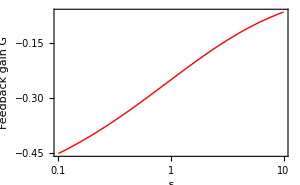

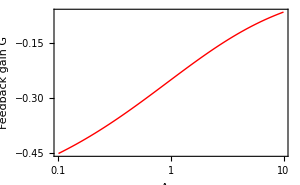

```mathematica
(*Negative positive feedback*)

gx=y/(y+Kyx);gy=Kxy/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fxyp=αx*Kyx/(yav+Kyx)^2;fyxp=-αy*Kxy/(xav+Kxy)^2;

G=fxyp*fyxp/(βx*βy);

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

LogLinearPlot[{G},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Feedback gain G"},ImageSize->300,PlotRange->All]
t13=Table[{δ,G},{δ,δi,δf,0.01}];
tp13=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"\n"]&/@t13];
(*Export["D:\\nashitarahman\\NP13g.dat",tp13,"FieldSeparators"->"    "];*)

Clear[βx,βy,Kxy,Kyx];

(*Parameters*)
βx=0.1*Sqrt[aτ]; βy=0.1/Sqrt[aτ];
Kyx=50; Kxy=50;

aτi=0.1;aτf=10;

LogLinearPlot[{G},{aτ,aτi,aτf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"A_τ","Feedback gain G"},ImageSize->300,PlotRange->All]
t14=Table[{aτ,G},{aτ,aτi,aτf,0.01}];
tp14=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"\n"]&/@t14];
(*Export["D:\\nashitarahman\\NP14g.dat",tp14,"FieldSeparators"->"    "];*)

Quit[];
```

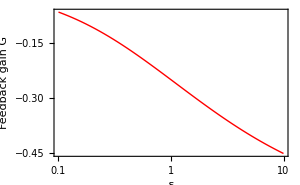

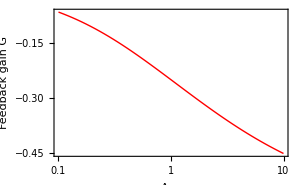

```mathematica
(*Positive negative feedback*)
gx=Kyx/(y+Kyx);gy=x/(x+Kxy);

xdot=αx*gx-βx*x;
ydot=αy*gy-βy*y;

sol=Solve[{xdot==0,ydot==0},{x,y}];

xav=x/.sol[[2,1]];
yav=y/.sol[[2,2]];

fxyp=-αx*Kyx/(yav+Kyx)^2;fyxp=αy*Kxy/(xav+Kxy)^2;

G=fxyp*fyxp/(βx*βy);

(*========================Data Extraction formatting===============================*)
toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];
(*================================================================================*)

(*Parameters*)
αx=10; αy=10;
βx=0.1; βy=0.1;
Kyx=50/Sqrt[δ]; Kxy=50*Sqrt[δ];

δi=0.1;δf=10;

LogLinearPlot[{G},{δ,δi,δf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"δ","Feedback gain G"},ImageSize->300,PlotRange->All]
t13=Table[{δ,G},{δ,δi,δf,0.01}];
tp13=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"\n"]&/@t13];
(*Export["D:\\nashitarahman\\PN13g.dat",tp13,"FieldSeparators"->"    "];*)

Clear[βx,βy,Kxy,Kyx];

(*Parameters*)
βx=0.1*Sqrt[aτ]; βy=0.1/Sqrt[aτ];
Kyx=50; Kxy=50;

aτi=0.1;aτf=10;

LogLinearPlot[{G},{aτ,aτi,aτf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"A_τ","Feedback gain G"},ImageSize->300,PlotRange->All]
t14=Table[{aτ,G},{aτ,aτi,aτf,0.01}];
tp14=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"\n"]&/@t14];
(*Export["D:\\nashitarahman\\PN14g.dat",tp14,"FieldSeparators"->"    "];*)

Quit[];
```